# Examples and extended examples of RISP Dynamics

## Example 2.1

```mathematica
fave[z_, w_]:=-(2 z w - z - w)/(2 - z - w);
```

## Compute fixed point curves

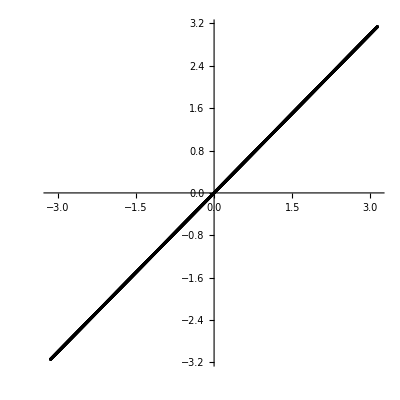

```mathematica
curve[z_]= w/.Solve[fave[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All]
```

## Compute evolution of vertical lines

```mathematica
Fave[{z_, w_}] := { -(2 z w - z - w)/(2 - z - w), w}
```

```mathematica
input = Table[{Exp[ s I], Exp[I  t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Fave], input[[i]],1]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation frames

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Fave], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

### Animation export

```mathematica
Export["fave_fixed.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

amy_fixed_fixed.gif

## Example 2.2

```mathematica
vert[z_, w_]:=-(3 z w - z - w - 1)/(3 - z - w - z w);
```

## Compute fixed point curves

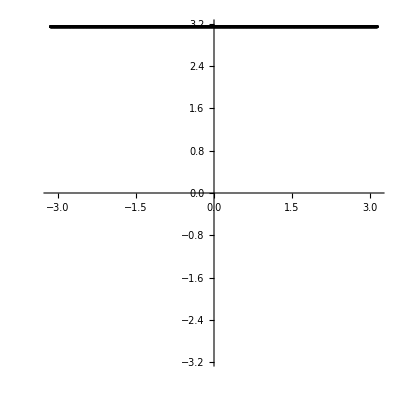

```mathematica
curve[z_]= w/.Solve[vert[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->{{-Pi, Pi},{-Pi,Pi}}]
```

## Compute evolution of vertical lines

```mathematica
Vert[{z_, w_}] := { -(3 z w - z - w - 1)/(3 - z - w - z w), w}
```

```mathematica
input = Table[{Exp[ s I], Exp[I  t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Vert], input[[i]],1]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation frames

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Vert], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

### Animation export

```mathematica
Export["vert.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

amy_fixed_fixed.gif

## Example 2.3

```mathematica
nosing[z_, w_]:=(3 z w - z - w )/(3 - z - w );
```

## Compute fixed point curves

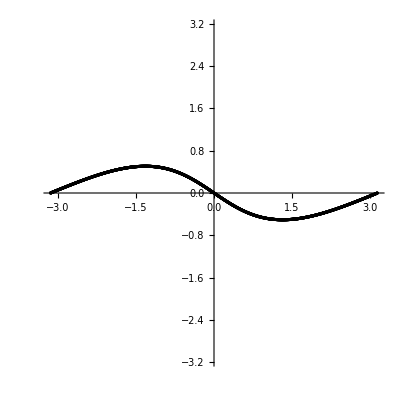

```mathematica
curve[z_]= w/.Solve[nosing[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->{{-Pi, Pi},{-Pi,Pi}}]
```

## Compute evolution of vertical lines

```mathematica
Nosing[{z_, w_}] := { (3 z w - z - w )/(3 - z - w ), w}
```

```mathematica
input = Table[{Exp[ s I], Exp[I  t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Nosing], input[[i]],1]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation frames

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Nosing], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

### Animation export

```mathematica
Export["vert.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

amy_fixed_fixed.gif

## Example 4.4

```mathematica
zfave[z_, w_]:=-z(2 z w - z - w )/(2 - z - w );
```

## Compute fixed point curves

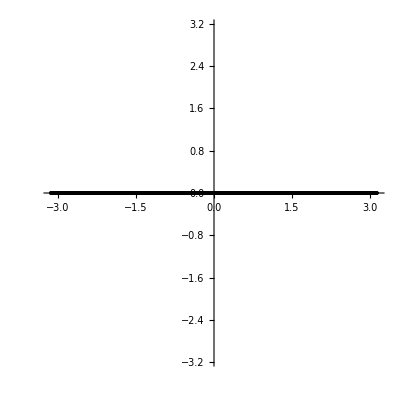

```mathematica
curve[z_]= w/.Solve[zfave[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->{{-Pi, Pi},{-Pi,Pi}}]
```

## Compute evolution of vertical lines

```mathematica
Zfave[{z_, w_}] := {-z(2 z w - z - w )/(2 - z - w ), w}
```

```mathematica
input = Table[{Exp[ s I], Exp[I  t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Nosing], input[[i]],1]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation frames

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Zfave], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

### Animation export

```mathematica
Export["vert.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

amy_fixed_fixed.gif

## Example 5.1

```mathematica
amy[z_, w_]:=-(4 w^2 z - w^2 - 3 z w - w +z)/(4 - 3 w - z - z w + w^2);
```

## Compute fixed point curves

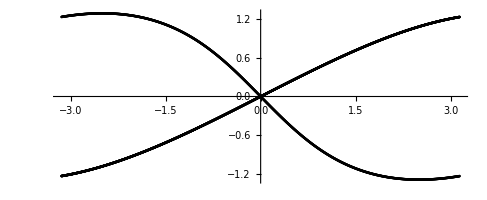

```mathematica
curve[z_]= w/.Solve[amy[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All]
```

## Compute evolution of vertical lines

```mathematica
Amy[{z_, w_}] := { -(4 w^2 z - w^2 - 3 z w - w +z)/(4 - 3 w - z - z w + w^2), w}
```

```mathematica
Amy[{z, w}]
```

{(w+w^2-z+3 w z-4 w^2 z)/(4-3 w+w^2-z-w z),w}

```mathematica
input = Table[{Exp[ s I], Exp[I  t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Amy], input[[i]],1]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation frames

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Amy], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

### Animation export

```mathematica
Export["amy_fixed.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

amy_fixed_fixed.gif

## Example 5.2:

```mathematica
mult[z_,w_]:= -(4 w^3 z - w^3 + w^2 - 3w - 1)/(4 - z+ z w - 3 w^2 z - w^3 z)
```

## Compute fixed point curves

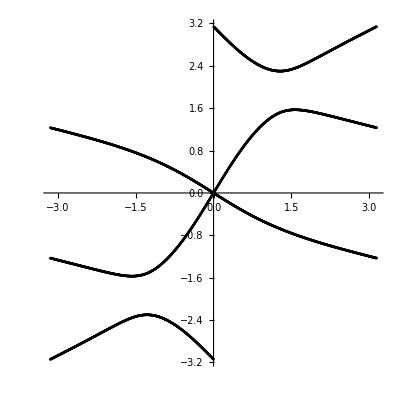

```mathematica
curve[z_]= w/.Solve[mult[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All]
```

## Compute evolution of lines

```mathematica
Mult[{z_, w_}] := {-(4 w^3 z - w^3 + w^2 - 3w - 1)/(4 - z+ z w - 3 w^2 z - w^3 z),w}
```

```mathematica
input = Table[{Exp[ s I],Exp[I t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Mult], input[[i]],7]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation frames

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Mult], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1];
```

### Animation export

```mathematica
Export["mult.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

switched_mult.gif

## Degree (2,2) RISP

```mathematica
twotwo[z_, w_]:=-(w + z - 3w^2 z - 3 w z^2 + 4 z^2 w^2)/(4 - 3z - 3w + w^2 z + w z^2)
```

## Find fixed curve

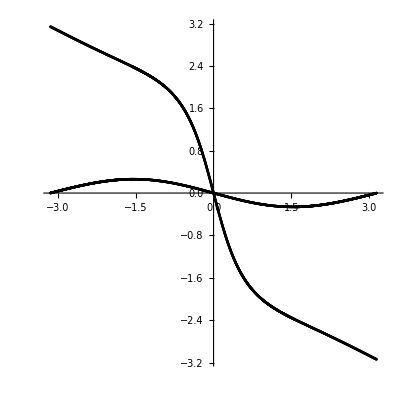

```mathematica
curve[z_]= w/.Solve[twotwo[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All]
```

## Compute evolution

```mathematica
Twotwo[{z_,w_}]:= {-(w + z - 3w^2 z - 3 w z^2 + 4 z^2 w^2)/(4 - 3z - 3w + w^2 z + w z^2),w}
```

```mathematica
input = Table[{Exp[ s I], Exp[I   t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.001}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Twotwo], input[[i]],5]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation frames

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Twotwo], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

```mathematica
Export["twotwo.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

twotwo_27.gif

## Degree (2, 4) RISP

```mathematica
input = Table[{Exp[ s I], Exp[I   t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.01}]//N;
```

```mathematica
big[z_, w_]:=-(-8-6 w-2 w^2+2 w^3-10 w^4+14 z-8 w z+36 w^2 z-32 w^3 z+38 w^4 z-6 z^2+10 w z^2-30 w^2 z^2+34 w^3 z^2-32 w^4 z^2)/(32-34 w+30 w^2-10 w^3+6 w^4-38 z+32 w z-36 w^2 z+8 w^3 z-14 w^4 z+10 z^2-2 w z^2+2 w^2 z^2+6 w^3 z^2+8 w^4 z^2)
```

## Fixed point curves

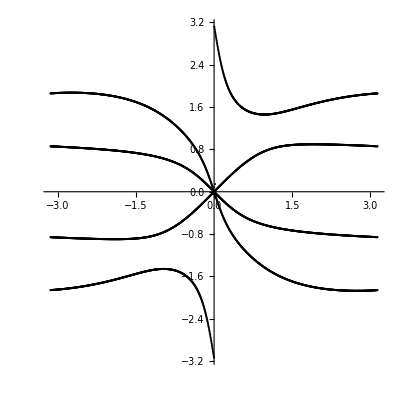

```mathematica
curve[z_]= w/.Solve[big[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All]
```

## Compute evolution

```mathematica
Big[{z_,w_}]:={-(-8-6 w-2 w^2+2 w^3-10 w^4+14 z-8 w z+36 w^2 z-32 w^3 z+38 w^4 z-6 z^2+10 w z^2-30 w^2 z^2+34 w^3 z^2-32 w^4 z^2)/(32-34 w+30 w^2-10 w^3+6 w^4-38 z+32 w z-36 w^2 z+8 w^3 z-14 w^4 z+10 z^2-2 w z^2+2 w^2 z^2+6 w^3 z^2+8 w^4 z^2),w}
```

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Big], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

### Export Animation

```mathematica
Export["beast_polynomial.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

beast_polynomial.gif

## Blaschke

```mathematica
a[z_]:=Times@@((z - #)/(1 - Conjugate[#]z))&@{.1, .2, .3}
c[z_]:=Times@@((z - #)/(1 - Conjugate[#]z))&@{.1, .2}
b[z_]:= Times@@((z - #)/(1 - Conjugate[#]z))& @{1/3 + 1/3 I, 1/3 + 1/3 I}
d[z_]:=Times@@((z - #)/(1 - Conjugate[#]z))&@{1/3 + 1/3 I, 1/3 + 1/3 I,1/3 + 1/3 I}
```

```mathematica
GraphicsRow[ComplexPlot[#, {z, 1}]&/@{a[z], b[z], c[z], d[z]}]
```

-Graphics-

```mathematica
f[{z_, w_}]:={a[z] b[w], c[z] d[w]}
```

```mathematica
input = Table[{Exp[ s I], Exp[I   t ] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

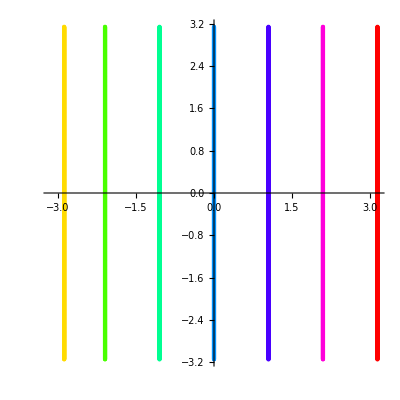

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full]
```

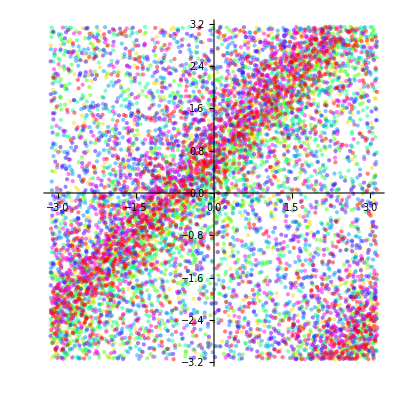

```mathematica
Show[Table[ListPlot[Arg[Nest[Map[f], input[[i]],4]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

```mathematica
abSmall = Table[Show[Table[ListPlot[Arg[Nest[Map[f], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

```mathematica
Export["blaschke_ex61.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

blaschke_ex61.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["blaschke_ex61.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["blaschke.gif"]]]
```

## Maximum rotation belts

```mathematica
bands[z_, w_]:= (2 z^2 w^3 - z^2 - w^3)/(2 - z^2 - w^3)
```

## Find fixed curve

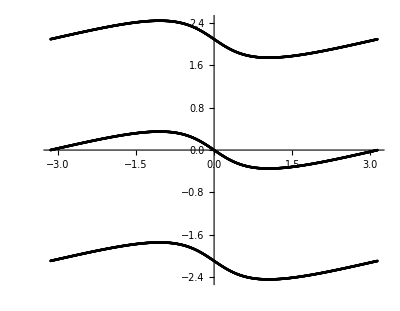

```mathematica
curve[z_]= w/.Solve[bands[z,w]==  z,w];
fixed=ListPlot[Table[Inner[List,Flatten[ConstantArray[t, {1,Length[curve[z]]}]],Arg[curve[Exp[I t]]], List], {t, Range[-Pi, Pi, .005]}], PlotStyle->{{Black}}, AspectRatio->Full, PlotRange->All]
```

## Compute evolution

```mathematica
Bands[{z_, w_}]:= {(2 z^2 w^3 - z^2 - w^3)/(2 - z^2 - w^3),w}
```

```mathematica
input = Table[{Exp[ s I], Exp[I   t] }, {s, { -11Pi/12, -2Pi/3, -Pi/3, 0, Pi/3, 2Pi/3, Pi}},{t, -Pi, Pi,.005}]//N;
```

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full];
```

```mathematica
Show[fixed,Table[ListPlot[Arg[Nest[Map[Bands], input[[i]],4]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small, Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

## Build animation

```mathematica
abSmall = Table[Show[{fixed,Table[ListPlot[Arg[Nest[Map[Bands], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

### Export animation

```mathematica
Export["rem210.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

rem210.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rem210.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rem210.gif"]]]
```

## Singular inner function

```mathematica
singular[z_,w_]:= Exp[-(1 + z w)/(1-z w)]
```

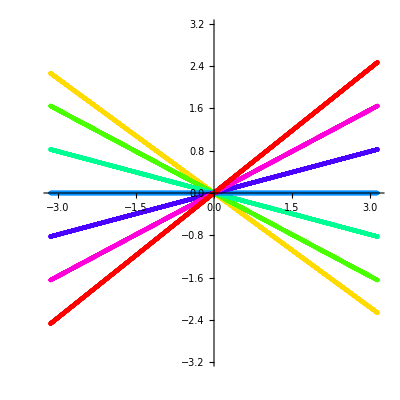

```mathematica
frame1 =Show[Table[ListPlot[Arg[input[[i]]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}},PlotStyle->{Hue[i/7], PointSize->Small}],{i, 1, 7}], AspectRatio->Full]
```

```mathematica
Sing[{z_, w_}]:= {Exp[-(1 + z w)/(1-z w)], w}
```

```mathematica
Show[Table[ListPlot[Arg[Nest[Map[Sing], input[[i]],6]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}],Axes->True, AspectRatio->Full]
```

```mathematica
abSmall = Table[Show[{Table[ListPlot[Arg[Nest[Map[Sing], input[[i]],n]], PlotRange-> {{-Pi, Pi}, {-Pi, Pi}}, PlotStyle->{ PointSize->Small,Opacity[.5], Hue[i/7]}],{i, 1, 7}]},Axes->True, AspectRatio->Full],{n,1,10}]
```

```mathematica
PrependTo[abSmall, frame1]; (* adds initial lines *)
```

```mathematica
Export["sing.gif", abSmall, "AnimationRepetitions"-> ∞, "DisplayDurations"-> .3]
```

sing.gif